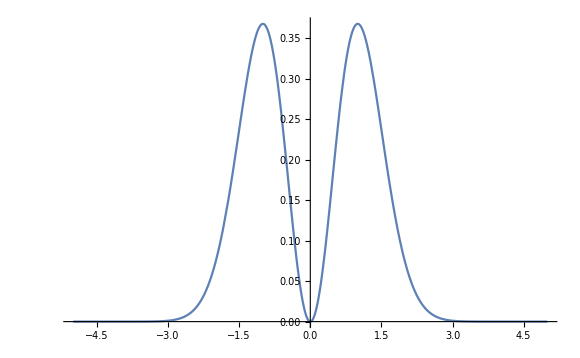

```mathematica
Plot[t^2*Exp[-t^2],{t, -5, 5}]
```

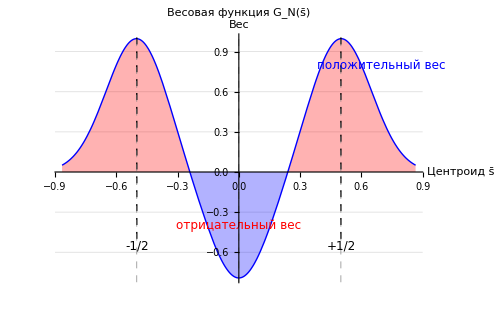

-Graphics-

```mathematica
(*Упрощённая модель весовой функции G_N(x)*)(*x—одномерный аналог центроида\bar{s}_z*)ClearAll[G,x,sigma,alpha]

(*Параметры*)
sigma=0.15;(*ширина пиков*)alpha=0.8;(*сила отрицательного пика в центре*)(*Весовая функция:два положительных пика при x=±0.5 и отрицательный при x=0*)G[x_]:=Exp[-(x-0.5)^2/(2 sigma^2)]+Exp[-(x+0.5)^2/(2 sigma^2)]-alpha*Exp[-x^2/(2 sigma^2)]

(*Область определения:центроид может быть от-0.866 до 0.866*)
xRange={-0.866,0.866};

(*График весовой функции*)
plot1=Plot[G[x],{x,xRange[[1]],xRange[[2]]},PlotStyle->{Blue,Thick},Filling->Axis,FillingStyle->{Directive[Blue,Opacity[0.3]],Directive[Red,Opacity[0.3]]},PlotLabel->Style["Весовая функция G_N(\!\(\* OverscriptBox[\(s\), \(_\)]\))",16,Bold],AxesLabel->{"Центроид \!\(\* OverscriptBox[\(s\), \(_\)]\)","Вес"},GridLines->{{-0.5,0,0.5},Automatic},GridLinesStyle->Directive[Gray,Dashed],Epilog->{Text[Style["положительный вес",Blue,12],{0.7,0.8}],Text[Style["отрицательный вес",Red,12],{0,-0.4}],{Dashed,Line[{{0.5,-0.5},{0.5,1.2}}],Line[{{-0.5,-0.5},{-0.5,1.2}}]},Text[Style["+1/2",12],{0.5,-0.55}],Text[Style["-1/2",12],{-0.5,-0.55}]},ImageSize->500]

(*Показать график*)
plot1
```